## Freshman Lab Presentation

I am going to talk about Gravity.

### Newton’s Gravity

Newton’s gravity is

F=G (M m)/r^2

Most of the time, we would like to discribe it in the language of energy, so we would like to have its potential

V=G (M m)/r

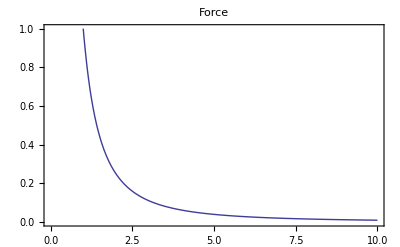

```mathematica
Plot[1/r^2,{r,0.1,10},PlotRange->{Automatic,{0,1}},Frame->True,PlotLabel->"Force"]
```

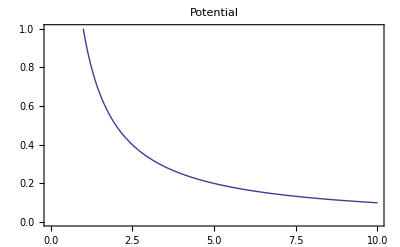

```mathematica
Plot[1/r,{r,0.1,10},PlotRange->{Automatic,{0,1}},Frame->True,PlotLabel->"Potential"]
```

Draw a figure of gravitation field

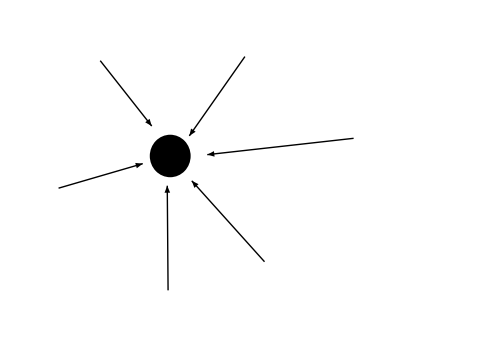

```mathematica
Import["http://upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Gravitymacroscopic.svg/500px-Gravitymacroscopic.svg.png"]
```

-Graphics-

#### Question 1: What are G and Mass

1. Does the mass at both sides of the kinetic equation for the particles equivalent?

F=m a  (Newton's second law of motion)
F = G (M m)/r^2
=> 
G (M m)/r^2=m a

SO we just assume that F is propotional to the mass we already know, mass defined by law of motion. We may think that there is only one kind of mass, which is called inertial mass. In this way, we have to make sure, or just make a statement that the gravitational force is propotional to inertial mass. But some people don’t agree. They think the mass in Newton’s theory might be diferent from inertial mass we already know. We can call the gravitational mass gravitational charge but the dimension of it is mass, [M]. Either way is OK as long as one can be consistent.

Then, are they the same mass? Galileo equivalence principle  indicates that they are the same because it says, point particles have the same acceleration when falling in gravitational field.

F=G (M_G m_G)/r^2
m_I a=G(M_G m_G)/r^2

That is just a defination of gravitation mass. We can test it. But, wait, what is that G?

2. Can we derive G theoretically?

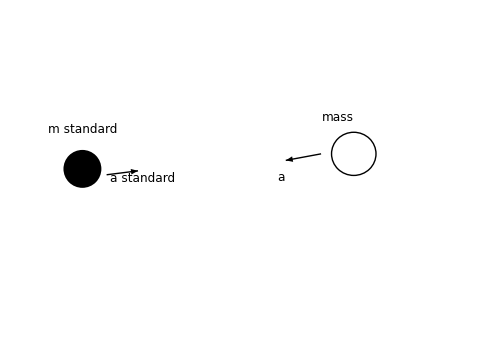

G=F/((m_G m_G)/r^2)

Since those are not fundamental quantities. So we have to get the answer by experiments. Torsion balance!

Comment:
We are not really sure about the equivalence of inertial mass and gravitational mass. Theories are still coming up.

#### Does it work in short distance and long distance?

Long distance, yes. Short? (I) Don’t know. It’s hard to test. Many forces will disturb our tests.

### Tidal force

Tidal force is very important in the theory of gravity.  Imagine we are in a roo,. And we are floating in the station. Are we free falling to a planet? Well we can find out by checking the tidal force.

```mathematica
Import["http://upload.wikimedia.org/wikipedia/commons/9/9a/Tidal-forces.png"]
Import["http://scienceblogs.com/startswithabang/files/2010/02/Field_tidal1.png"]
```

-Graphics-

-Graphics-

Then the water drop is experiencing a stronger force at the side near the sun. Equivalently, the drop will be stretched if it is free falling. Like this,

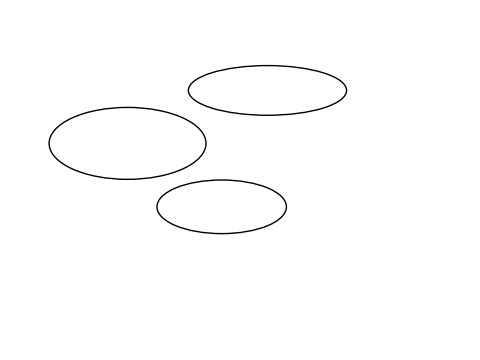

```mathematica
Import["http://upload.wikimedia.org/wikipedia/commons/thumb/7/71/Shoemaker-levy-tidal-forces.jpg/800px-Shoemaker-levy-tidal-forces.jpg"]
```

-Graphics-

Well, why is that important? We have a demonstration of gravitational field in a way like the electric field. BUT now, we are going to add more to this figure. The divergence of tidal force field is zero. (just like electric field, \nabla \cdot \vec E = 0 if there is no chare.)

```mathematica
Import["http://www4.nau.edu/meteorite/Meteorite/Images/tidalforce.gif"]
```

-Graphics-

We can add this to the previous figure of gravity.

And it is important because in GR we will need this information to write down the equation of motion.

### Summary

1. Newton’s gravitational law
2. Tidal force

## Draft

An object and a standard object moving towards eath other under gravitation:
m_s a_s = m_I a

Think about the object we  want to test, (put gravitation force in)

m_G=lim_(r→∞) ((a m_I r^2)/(m_s G))

Put everything together:

m_G=lim_(r→∞) ((a_s r^2)/G)